```mathematica
<<MaTeX`
```

```mathematica
(* MIXTUIRE UNIFORM GAMMA *)
F[x_, eta_, gamma_]:= Piecewise[{{ (1-eta) x  + eta x^gamma, 0  <= x  <= 1}},0]
```

```mathematica
delta[x_, lambda_, p_] :=Piecewise[{{x F[1- (lambda/Abs[x])^p , 1, 2], Abs[x]>lambda}},0]
```

```mathematica
p=Plot[{x,delta[x,2, 2],delta[x,2,1],delta[x,2,0.5]},{x,-6,6},AspectRatio->Automatic,AxesLabel->MaTeX[{"d","\\delta_{\\lambda, p, F}(d)"},Magnification->1.5],LabelStyle->{FontFamily->"Times New Roman",FontSize->14},TicksStyle->Directive[FontFamily->"Latin Modern Roman",FontSlant->"Plain",FontSize->11],PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Blue,Thick],Directive[Red,Thick],Directive[Green,Thick]},PlotLegends->Placed[Framed[LineLegend[{Directive[Black,Dotted,Thickness[0.003]],Directive[Blue,Thick],Directive[Red,Thick],Directive[Green,Thick]},MaTeX[{"\\delta=d","p = 2","p = 1","p = 0.5"},Magnification->1.2]],Background->Lighter[Gray,0.95],FrameStyle->Black,RoundingRadius->2],{0.2,0.8}]]
```

-Graphics-

```mathematica
Export["C:/Brani2/WorkTAMU/GRIT/Figs/mixtureug.png",p,ImageResolution->300]
Export["C:/Brani2/WorkTAMU/GRIT/Figs/mixtureug.pdf",p,ImageResolution->600]
```

C:/Brani2/WorkTAMU/GRIT/Figs/mixtureug.png

C:/Brani2/WorkTAMU/GRIT/Figs/mixtureug.pdf

```mathematica
"C:/Brani2/WorkTAMU/GRIT/Figs/mixtureugamma.png"
```

```mathematica
"C:/Brani2/WorkTAMU/GRIT/Figs/mixtureugamma.pdf"
```

```mathematica
Pprime[θ_,λ_]:=(2 λ (θ+2 λ+Sqrt[θ^2+4 λ θ])-λ^2)/(θ+2 λ+Sqrt[θ^2+4 λ θ])
```

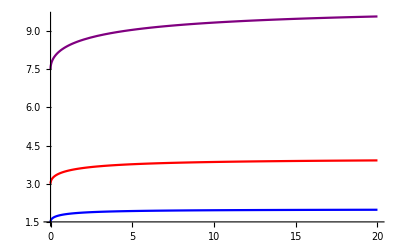

```mathematica
lamlist={1,2,5};

Plot[Evaluate@Table[Pprime[θ,λ],{λ,lamlist}],{θ,0,20},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]},AxesLabel->MaTeX[{"\\theta","P'(\\theta)"},Magnification->1.5],PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]},MaTeX[("\\lambda="<>ToString[#])&/@lamlist,Magnification->1.1]],Right],LabelStyle->{FontFamily->"Times New Roman",FontSize->14}]
```